# Color trajs based NNs, distances, etc.

Domain H from hidden_diff_eq_rhs notebook

```mathematica
domainH={{-1.5,1},{-0.5,2},{-0.1,0.2}};
```

```mathematica
spacingH={0.5,0.5,0.05};
```

```mathematica
domainHp={{-1.75,1.25},{-0.75,2.25},{-0.125,0.225}};
```

```mathematica
domainV={{-1.5,1},{-1.5,1},{-1.5,1}};
```

```mathematica
spacingV={0.5,0.5,0.5};
```

```mathematica
domainVp={{-1.75,1.25},{-1.75,1.25},{-1.75,1.25}};
```

Empty plot

```mathematica
makeEmpty[domain_,spacing_,label_]:=Module[
{npts,ptsEmptyH},
npts=2;
ptsEmptyH={};
Do[
Do[
Do[
AppendTo[ptsEmptyH,{x,y,z,0}];
,{z,domain[[3,1]],domain[[3,2]],(domain[[3,2]]-domain[[3,1]])/npts}];
,{y,domain[[2,1]],domain[[2,2]],(domain[[2,2]]-domain[[2,1]])/npts}];
,{x,domain[[1,1]],domain[[1,2]],(domain[[1,2]]-domain[[1,1]])/npts}];

Return[ListDensityPlot3D[ptsEmptyH,PlotRange->{domain[[1]]+0.5*spacing[[1]]*{-1,1},domain[[2]]+0.5*spacing[[2]]*{-1,1},domain[[3]]+0.5*spacing[[3]]*{-1,1}},OpacityFunctionScaling->False,OpacityFunction->Function[f,0.0],BaseStyle->{FontSize->24},AxesLabel->label,ImageSize->260]];
];
```

```mathematica
pEmptyH=makeEmpty[domainH,spacingH,{"b","W","b'"}];
```

```mathematica
pEmptyV=makeEmpty[domainV,spacingV,{"b","J","K"}];
```

Colors from NNs moment

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
getNoNNs[iIC_,iLatt_]:=Module[
{dat,dists},
SetDirectory[NotebookDirectory[]];
dat=Import["../../bimol_train_stoch_sim/data/ic_v"<>IntegerString[iIC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/0000.txt","Table"][[;;,1]];
dists=dat[[2;;]]-dat[[;;-2]];
Return[Length[Select[dists,#==1&]]];
];
```

```mathematica
makeColPlotH[icStart_,icEnd_,domain_]:=Module[
{avgs,initH,avgsC,cols,size,p1}
,
avgs=Association[];
Monitor[
Do[
avgs[iIC]={};
Do[
AppendTo[avgs[iIC],getNoNNs[iIC,iLatt]];
,{iLatt,1,50}];
avgs[iIC]=Mean[avgs[iIC]]//N;
,{iIC,icStart,icEnd}];
,ProgressIndicator[iIC,{icStart,icEnd}]];

initH={};
Do[
AppendTo[initH,{Transpose[Import["../../bimol_train_stoch_sim/data/ic_v"<>IntegerString[iIC,10,3]<>"/init_hidden.txt","Table"]][[2]]}]
,{iIC,icStart,icEnd}];

avgsC=Values[avgs];
avgsC-=Min[avgsC];
avgsC/=Max[avgsC]//N;

cols=ColorData[10,"ColorList"][[Round[10#]+1]]&/@avgsC;

size=Table[(domain[[i,2]]-domain[[i,1]])/25.0,{i,1,3}];
p1=Show[Graphics3D[Table[{EdgeForm[None],cols[[i]],Ellipsoid[initH[[i,1]],size]},{i,Length[initH]}]],PlotRange->domain];

Return[{p1,avgsC,avgs}]
];
```

```mathematica
makeColPlotV[icStart_,icEnd_,domainV_,avgsC_]:=Module[
{initH,cols,size,initV,p2}
,
cols=ColorData[10,"ColorList"][[Round[10#]+1]]&/@avgsC;

initV={};
Do[
AppendTo[initV,{Transpose[Import["../../bimol_train_stoch_sim/data/ic_v"<>IntegerString[i,10,3]<>"/init_visible.txt","Table"]][[2]]}]
,{i,icStart,icEnd}];

size=Table[(domainV[[i,2]]-domainV[[i,1]])/25.0,{i,1,3}];
p2=Show[Graphics3D[Table[{EdgeForm[None],cols[[i]],Ellipsoid[initV[[i,1]],size]},{i,Length[initV]}]],PlotRange->domainV];

(*p2=ListPointPlot3D[initV,PlotStyle->cols]*)

Return[p2]
];
```

```mathematica
{p1,avgsC,avgs}=makeColPlotH[1,50,domainH];
```

```mathematica
p1Full=Show[pEmptyH,p1]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/nns_hidden.pdf",p1Full]
```

../figures/nns_hidden.pdf

```mathematica
p2=makeColPlotV[1,50,domainV,avgsC];
```

```mathematica
p2Full=Show[pEmptyV,p2]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/nns_visible.pdf",p2Full]
```

../figures/nns_visible.pdf

```mathematica
legnns=BarLegend[{ColorData[10,"ColorList"],{avgs[[1]],avgs[[-1]]}},LabelStyle->{FontSize->24}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/nns_leg.pdf",legnns]
```

../figures/nns_leg.pdf

Show trajs

```mathematica
trajs={};
SetDirectory[NotebookDirectory[]];
Do[
d1=Import["../../bimol_train/data_learned_hidden/trajs/hA_"<>IntegerString[i,10,3]<>".txt","Table"][[;;,2]];
d2=Import["../../bimol_train/data_learned_hidden/trajs/wAX_"<>IntegerString[i,10,3]<>".txt","Table"][[;;,2]];
d3=Import["../../bimol_train/data_learned_hidden/trajs/bX_"<>IntegerString[i,10,3]<>".txt","Table"][[;;,2]];
AppendTo[trajs,Transpose[{d1,d2,d3}]];
,{i,icStart,icEnd}];
```

```mathematica
colsTraj=Map[ColorData[{"StarryNightColors","Reverse"}][#*0.7+0.25]&,avgsC]
```

{RGBColor[0.5800382049918064, 0.6987564991806379, 0.6359335980335308],RGBColor[0.8103628257741922, 0.8388010663221144, 0.6222266572713139],RGBColor[0.7051052543804361, 0.7838447713769486, 0.6472450513046767],RGBColor[0.20277728041514348, 0.3200212240850456, 0.36066656781377365],RGBColor[0.8055273629564268, 0.8367538570107987, 0.6243661009286104],RGBColor[0.6610132784822892, 0.7538471815622505, 0.6432572357494013],RGBColor[0.8041518793982941, 0.8361715130131518, 0.6249746816757007],RGBColor[0.8423250931971932, 0.8523330598344467, 0.6080849974368671],RGBColor[0.866077, 0.862389, 0.597576],RGBColor[0.4174412170679442, 0.565868254212362, 0.5675624169082736],RGBColor[0.8040951584268247, 0.8361474988276818, 0.6249997777889827],RGBColor[0.17043687204672467, 0.2716224533972016, 0.3146160773645952],RGBColor[0.37773794229169305, 0.5272318010840793, 0.53966264020337],RGBColor[0.7780885930081096, 0.825136994789697, 0.6365063457288122],RGBColor[0.4893667424429598, 0.6249143811420648, 0.5984391370729862],RGBColor[0.8312786840035296, 0.8476562972141686, 0.6129724654985503],RGBColor[0.4538917116601539, 0.5957917135005674, 0.5832101541409304],RGBColor[0.6298413697970503, 0.7326396463716963, 0.6404379512920712],RGBColor[0.6928641396949452, 0.7755166361611833, 0.6461379267868398],RGBColor[0.8323563824614479, 0.8481125667380982, 0.612495639346191],RGBColor[0.6479933653094667, 0.744989197613345, 0.6420796742720283],RGBColor[0.12359008000000003, 0.20141280000000006, 0.2526644],RGBColor[0.8269253494432539, 0.8458132084793478, 0.6148985921929493],RGBColor[0.6478935193495525, 0.7449212682885836, 0.6420706438926005],RGBColor[0.6694003391150889, 0.7595532448422203, 0.6440157876213286],RGBColor[0.7098978604563217, 0.7871053789655028, 0.6476785095172066],RGBColor[0.49770795338459606, 0.6317619668557504, 0.6020199136434304],RGBColor[0.8028047563258961, 0.8356011761082398, 0.6255707143661499],RGBColor[0.5687575520736166, 0.6900890155720829, 0.6325206095382159],RGBColor[0.15984513767469227, 0.2557485383083324, 0.3006092333123241],RGBColor[0.35190255794781294, 0.5006160857178873, 0.5188589478633556],RGBColor[0.19695528238161272, 0.31131323290894586, 0.3521481627211228],RGBColor[0.7463673897138535, 0.811707061565612, 0.6505413470818102],RGBColor[0.6672037279969747, 0.7580587996974663, 0.643817119273919],RGBColor[0.28337441555527537, 0.43001812176982224, 0.46367732671961004],RGBColor[0.44164864548090255, 0.5857409612000505, 0.5779543603680827],RGBColor[0.15287890907012905, 0.24530819705029633, 0.29139687259128544],RGBColor[0.7696655287449052, 0.8215708882474053, 0.6402331185511997],RGBColor[0.597910631816463, 0.7109158483129544, 0.6375500359510904],RGBColor[0.8275634603722846, 0.8460833680658851, 0.614616260918526],RGBColor[0.8279463269297029, 0.8462454638178074, 0.614446862153872],RGBColor[0.6066371687129711, 0.7168528712971133, 0.638339291113072],RGBColor[0.5698126455817472, 0.6909551779654608, 0.6329735478633557],RGBColor[0.7391726959031892, 0.8070222569855876, 0.6503262167654104],RGBColor[0.17490577341568977, 0.27832003080801726, 0.32052589367620493],RGBColor[0.4836732189839909, 0.6202403727551578, 0.5959949793184588],RGBColor[0.8080939869154166, 0.8378404989033152, 0.6232305018025968],RGBColor[0.15608819363166526, 0.2501179769065928, 0.29564093185427964],RGBColor[0.658257529988655, 0.751972332198832, 0.6430079972771965],RGBColor[0.23453537149460063, 0.3675219575612421, 0.4071331387789403]}

```mathematica
p=ListPointPlot3D[trajs,PlotStyle->colsTraj,PlotRange->All]/.Point->Line;
```

```mathematica
Show[{pEmptyH,p1,p},PlotRange->All,ImageSize->500]
```

-Graphics3D-

```mathematica
trajsIdxsSort=SortBy[Range[1,50],avgsC[[#]]&]
```

{9,8,20,16,41,40,23,2,47,5,7,11,28,14,38,33,44,26,3,19,25,34,6,49,21,24,18,42,39,1,43,29,27,15,46,17,36,10,13,31,35,50,4,32,45,12,30,48,37,22}

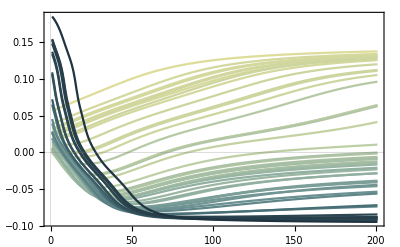

```mathematica
pltCompBp=ListLinePlot[trajs[[trajsIdxsSort,;;,3]],PlotStyle->Reverse[Sort[colsTraj]],PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/comp_bp.pdf",pltCompBp]
```

../figures/comp_bp.pdf

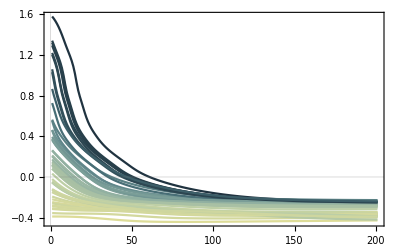

```mathematica
pltCompW=ListLinePlot[trajs[[;;,;;,2]],PlotStyle->colsTraj,PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/comp_W.pdf",pltCompW]
```

../figures/comp_W.pdf

OLD: Colors from average particle-particle distance

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
getAvgDist[iIC_,iLatt_]:=Module[
{dat,dists},
dat=Import["../data/ic_v"<>IntegerString[iIC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/0000.txt","Table"][[;;,1]];

dists=dat[[2;;]]-dat[[;;-2]];
Return[Mean[dists]//N];
];
```

```mathematica
icStart=1;
icEnd=50;
```

```mathematica
avgs=Association[];
Monitor[
Do[
avgs[iIC]={};
Do[
AppendTo[avgs[iIC],getAvgDist[iIC,iLatt]];
,{iLatt,1,50}];
avgs[iIC]=Mean[avgs[iIC]];
,{iIC,icStart,icEnd}];
,ProgressIndicator[iIC,{icStart,icEnd}]]
```

```mathematica
avgs
```

<|1→1.56899,2→2.81243,3→1.8362,4→1.09475,5→2.39955,6→1.78539,7→2.51874,8→2.78795,9→3.49951,10→1.40574,11→2.712,12→1.05138,13→1.31669,14→2.1078,15→1.4607,16→2.98842,17→1.47319,18→1.7351,19→2.10363,20→2.66644,21→1.78039,22→1.,23→3.11756,24→1.77964,25→1.84839,26→1.98728,27→1.4642,28→2.38561,29→1.68839,30→1.0376,31→1.33752,32→1.08774,33→1.92778,34→1.80005,35→1.21131,36→1.37785,37→1.02993,38→2.0479,39→1.71648,40→2.85386,41→2.95286,42→1.64049,43→1.58781,44→2.11088,45→1.05347,46→1.49665,47→2.324,48→1.03318,49→1.74726,50→1.1549|>

```mathematica
initH={};
Do[
AppendTo[initH,{Transpose[Import["../data/ic_v"<>IntegerString[iIC,10,3]<>"/init_hidden.txt","Table"]][[2]]}]
,{iIC,icStart,icEnd}];
```

```mathematica
avgsC=Values[avgs];
avgsC-=Min[avgsC];
avgsC/=Max[avgsC];
```

```mathematica
cols=ColorData[10,"ColorList"][[Round[10#]+1]]&/@avgsC
```

{RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786]}

```mathematica
avgsC
```

{0.227641,0.725113,0.334545,0.0379062,0.559928,0.314218,0.607615,0.71532,1.,0.162326,0.684933,0.0205579,0.126701,0.443208,0.184317,0.795524,0.189314,0.294096,0.441539,0.666705,0.312215,0.,0.84719,0.311918,0.339421,0.394989,0.185716,0.554352,0.275411,0.015044,0.135033,0.0351022,0.371185,0.320081,0.0845408,0.151169,0.0119724,0.419242,0.286646,0.741687,0.781295,0.256244,0.235169,0.44444,0.0213913,0.1987,0.529704,0.0132728,0.298964,0.0619719}

```mathematica
p1=ListPointPlot3D[initH,PlotStyle->cols]
```

-Graphics3D-

```mathematica
initV={};
Do[
AppendTo[initV,{Transpose[Import["../data/ic_v"<>IntegerString[i,10,3]<>"/init_visible.txt","Table"]][[2]]}]
,{i,icStart,icEnd}];
```

```mathematica
p2=ListPointPlot3D[initV,PlotStyle->cols]
```

-Graphics3D-